```mathematica
Needs["MaTeX`"]
```

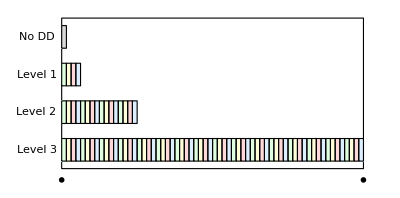

```mathematica
p3=Module[{L=8, h=-1,hp=0.2,level=3,dL,colors},
colors={LightGreen,LightYellow,LightRed,LightBlue};
dL=L/4^level;
Graphics[{
EdgeForm[Black],FaceForm[White],Rectangle[{0,0},{L,-level-1}],
FaceForm[LightGray],Rectangle[{0,-hp},{dL ,h+hp}],
Table[{FaceForm[colors[[Mod[m,4]+1]]],Rectangle[{m dL,n h- hp},{(m+1)dL,(n+1)h+hp}]},{n,1,level},{m,0,4^n-1}],
Text["No DD",{-1/12L,(1/2) h}],
Table[Text["Level "<>ToString[n],{-1/12L,(n+1/2) h}],{n,1,level}],
Text[MaTeX["0",Magnification->1.25],{0,4.3 h}],Text[MaTeX["4^n \\tau",Magnification->1.25],{L,4.3 h}]
}]
]
```

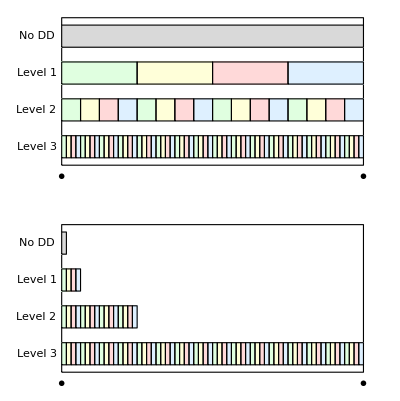

```mathematica
p23=GraphicsColumn[{p2,p3}]
```

```mathematica
Export[NotebookDirectory[]<>"memory-vs-computation.pdf",p23]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/memory-vs-computation.pdf

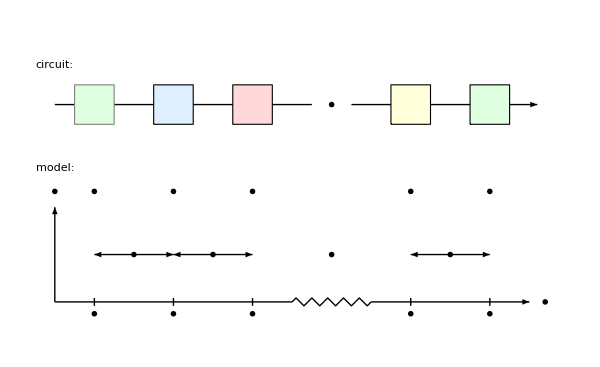
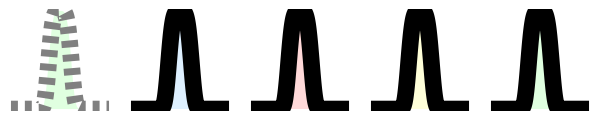

```mathematica
p4=Module[{
L=5,
tmin=-1.5,
tdash=0.75,
dt={1,0},
pulsew=0.2,
pulseh=1.2,
hoff=0.3,
voff=0.2,
eps=0.1,
hg=2.5,
op=Magnification->1.75,
p0,pt,v,p,tick,zigzag,pulse,twoarrows,gate},

p0={0,0};
pt={-L,0};

tick[x_,label_,h_:0.05]:={
Line[{{x,-h},{x,h}}],
Text[MaTeX[label,op],{x,-h-2h}]
};

zigzag[x1_,x2_,n_,amp_,y_:0]:=Module[{dx=(x2-x1)/(4n)},
Table[Line[{{x1+i*4dx,y},{x1+i*4dx+dx,y+amp},{x1+i*4dx+2dx,y},{x1+i*4dx+3dx,y-amp},{x1+(i+1)*4dx,y}}],{i,0,n-1}]];

twoarrows[x1_,x2_,label_]:={
Arrowheads[{-0.02,0.02}],Arrow[{{x1,pulseh/2},{x2,pulseh/2}}],
Text[MaTeX[label,op],{(x1+x2)/2,pulseh/2},Background->White]
};

pulse[x_,label_,color_,edge_:Black]:=
{
Text[MaTeX[label,op],{x,pulseh+voff}],
Inset[Plot[E^(-t^4),{t,-4,4},Axes->None,PlotRange->{0,1},Filling->Axis,
AspectRatio->pulseh/(2pulsew),PlotStyle->Directive[edge,Thickness[Scaled[0.03]]],FillingStyle->color
],{x,0},{0,0},{Automatic,pulseh}]
};

gate[x_,y_,label_,color_,edge_:Black,l_:0.5]:=
{color,EdgeForm[edge],
Rectangle[{x-0.5l,y-0.5l},{x+0.5l,y+0.5l},RoundingRadius->0.1l],
Text[MaTeX[label,op],{x,y}]};

Graphics[{
Line[{{-0.5,hg},{2.75,hg}}],
Text[MaTeX["\\cdots",op],{3,hg}],
Arrowheads[0.025],
Arrow[{{3.25,hg},{5.6,hg}}],
Text[Style["circuit:",Magnification->1.75,FontFamily->"Times"],{-0.5,hg+0.5}],
gate[0,hg,"",LightGreen,{Gray,Dashed}],
gate[1,hg,"P_1",LightBlue],
gate[2,hg,"P_2",LightRed],
gate[4,hg,"P_{L-1}",LightYellow],
gate[5,hg,"P_L",LightGreen],
Text[Style["model:",Magnification->1.75,FontFamily->"Times"],{-0.5,pulseh+0.5}],
Line[{{-0.5,0},{2.5,0}}],
zigzag[2.5,3.5,5,0.05],
Arrow[{{3.5,0},{5.5,0}}],Text[MaTeX["t",op],{5.5+voff,0}],
Arrow[{{-0.5,0.},{-0.5,1pulseh}}],Text[MaTeX["H_{\\mathrm{ctrl}}",op],{-0.5,pulseh+voff}],

tick[0,"t_0"],pulse[0,"",LightGreen,{Dashed,Gray}],twoarrows[0,1,"\\tau"],
tick[1,"t_1"],pulse[1,"P_1",LightBlue],twoarrows[1,2,"\\tau"],
tick[2,"t_2"],pulse[2,"P_2",LightRed],Text[MaTeX["\\cdots",op],{3,0.5 pulseh}],
tick[4,"t_{L-1}"],pulse[4,"P_{L-1}",LightYellow],twoarrows[4,5,"\\tau"],
tick[5,"t_{L}"],pulse[5,"P_{L}",LightGreen]
},ImageSize->600,PlotRange->{Automatic,{0-2voff,3+2voff}}]

]
```

```mathematica
Export[NotebookDirectory[]<>"pulse.pdf",p4]
"/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf"
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf

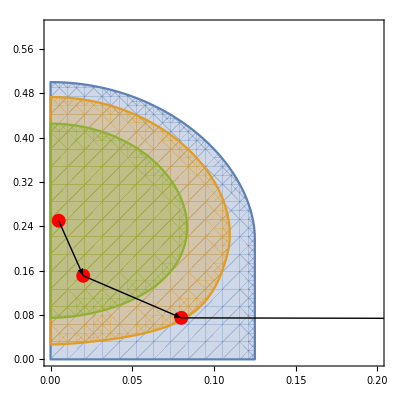

```mathematica
p5=Module[{iter,cddpts1,cddpts2,op},
iter[{α_,β_},η_]:={4α,8α β fpdd[β/α]+(η)*8/π};
cddpts1=NestList[iter[##,0.01]&,{0.005,0.25},4];
(*cddpts2=NestList[iter[##,0.025]&,{0.005,0.25},4];*)
op=Magnification->1.5;
Show[RegionPlot[ {
(π/8)(β-8α β fpdd[β/α])>=0.0,
(π/8)(β-8α β fpdd[β/α])>=0.01,
(π/8)(β-8α β fpdd[β/α])>=0.025
},{α,0.0,0.2},{β,0.0,0.6},
ImageSize->400,
FrameTicksStyle->Directive[16,FontFamily->"Times"],
PlotLegends->{MaTeX["\\eta=0",op],MaTeX["\\eta=0.01",op],MaTeX["\\eta=0.1",op]}],
ListPlot[cddpts1,PlotStyle->{PointSize[0.025],Red}],
(*ListPlot[cddpts2,PlotStyle->{PointSize[0.025],Red}],*)
Graphics[{
Arrow[cddpts1[[1;;2]]],
Arrow[cddpts1[[2;;3]]],
Arrow[cddpts1[[3;;4]]]
}]
(*Graphics[{
Arrow[cddpts2[[1;;2]]],
Arrow[cddpts2[[2;;3]]],
Arrow[cddpts2[[3;;4]]]
}]*)
]]
```

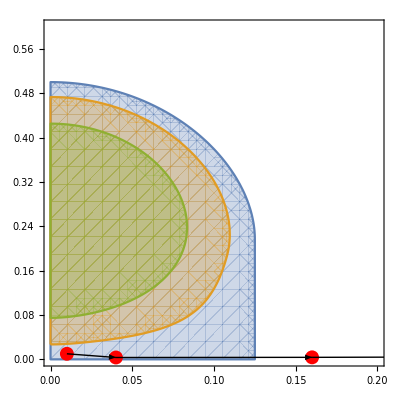

```mathematica
p5=Module[{iter,cddpts1,cddpts2,op},
iter[{α_,β_},η_]:={4α,8α β fpdd[β/α]+(η)*8/π};
cddpts1=NestList[iter[##,0.001]&,{0.01,0.01},4];
(*cddpts2=NestList[iter[##,0.025]&,{0.005,0.25},4];*)
op=Magnification->1.5;
Show[RegionPlot[ {
(π/8)(β-8α β fpdd[β/α])>=0.0,
(π/8)(β-8α β fpdd[β/α])>=0.01,
(π/8)(β-8α β fpdd[β/α])>=0.025
},{α,0.0,0.2},{β,0.0,0.6},
ImageSize->400,
FrameTicksStyle->Directive[16,FontFamily->"Times"],
PlotLegends->{MaTeX["\\eta=0",op],MaTeX["\\eta=0.01",op],MaTeX["\\eta=0.1",op]}],
ListPlot[cddpts1,PlotStyle->{PointSize[0.025],Red}],
(*ListPlot[cddpts2,PlotStyle->{PointSize[0.025],Red}],*)
Graphics[{
Arrow[cddpts1[[1;;2]]],
Arrow[cddpts1[[2;;3]]],
Arrow[cddpts1[[3;;4]]]
}]
(*Graphics[{
Arrow[cddpts2[[1;;2]]],
Arrow[cddpts2[[2;;3]]],
Arrow[cddpts2[[3;;4]]]
}]*)
]]
```

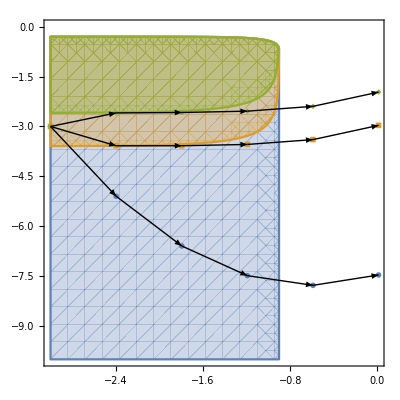

```mathematica
p6=Module[{iter,cddpts1,cddpts2,cddpts3,
init={10^(-3),10^(-3)},
noise=10^(-4),op=Magnification->1.5},
iter[{α_,β_},η_]:={4α,8α β fpdd[β/α]+(η)*8/π};
cddpts1=Log[10,NestList[iter[##,0]&,init,5]];
cddpts2=Log[10,NestList[iter[##,noise]&,init,5]];
cddpts3=Log[10,NestList[iter[##,10noise]&,init,5]];

Show[
RegionPlot[ {
{(π/8)(10^b-8*10^(a+b)  fpdd[10^(b-a)])≥0,
(π/8)(10^b-8*10^(a+b)  fpdd[10^(b-a)])≥noise,
(π/8)(10^b-8*10^(a+b)  fpdd[10^(b-a)])≥10noise}
},{a,-3,0},{b,-10,0},
FrameLabel->{MaTeX["\\log_{10}\\Phi_\\mathrm{B}",op],MaTeX["\\log_{10}\\Phi_\\mathrm{SB}",op]},ImageSize->400,
FrameTicksStyle->Directive[16,FontFamily->"Times"],
PlotRangePadding->0,
PlotLegends->{MaTeX["\\eta=0",op],MaTeX["\\eta=10^{-4}",op],MaTeX["\\eta=10^{-3}",op]}],
ListPlot[{cddpts1,cddpts2,cddpts3},PlotMarkers->{Automatic,Scaled[0.04]}],
Graphics[
{Table[Arrow[cddpts1[[n;;n+1]]],{n,1,5}],
Table[Arrow[cddpts2[[n;;n+1]]],{n,1,5}],
Table[Arrow[cddpts3[[n;;n+1]]],{n,1,5}]}
]]
]
```

```mathematica
Export[NotebookDirectory[]<>"cddevo.pdf",p6]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/cddevo.pdf

```mathematica
4^(-6.)
```

0.000244141

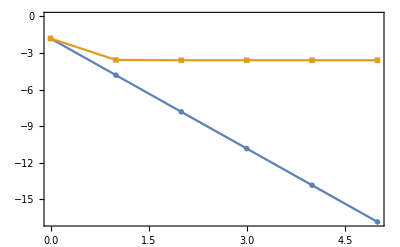

```mathematica
p7=Module[{iter,cddpts1,cddpts2,
init={2*4^(-5),4^(-3)},
noise=10^(-4),op=Magnification->1.5},
iter[{α_,β_},η_]:={α,1/2α β +(η)*8/π};
cddpts1=Log10[NestList[iter[##,0]&,init,5]];
cddpts2=Log10[NestList[iter[##,noise]&,init,5]];

Show[
ListPlot[
{Transpose[{Range[0,5],cddpts1[[All,2]]}],
Transpose[{Range[0,5],cddpts2[[All,2]]}]},
PlotMarkers->{Automatic,Scaled[0.04]},
PlotRange->All,
Joined->True,
Frame->True,
FrameLabel->{"Concatenation level",MaTeX["\\log_{10}\\Phi_\\mathrm{SB}",op]}
]
]
]
```